# Elliptic Constraints

The plan is to build ellipsoidal constraints out of fully nonlinear constraints
	g_i(x)≥0	
The first thing to do is to build ellipsoidal constraints for a few linear constraints
	c_i+d_i.x≥0. 
The assumption is that we have an interior feasible point
	c_i+d_i.z>0 
and want to build an ellipsoidal constraint
	(x-z).B.(x-z)<Δ
entirely within the feasible set.

Old Pics

## 2 Constraints in 2D

Assuming the center point is at the origin.

{0.644721,0.756853}

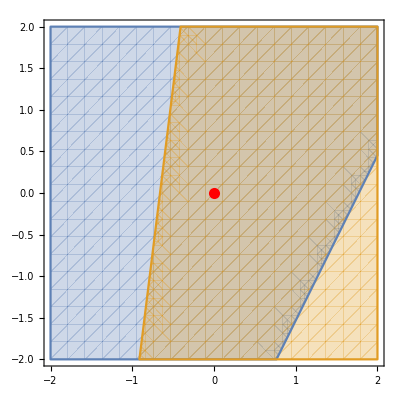

```mathematica
{c1,c2}=RandomReal[{0,1.8},2]
{d1,d2}=RandomReal[{-1,1},{2,2}];
RegionPlot[ {c1+d1.{x,y}>0, c1+d2.{x,y}>0}, {x,-2,2},{y,-2,2},
Epilog->{
{Red,PointSize[0.02],Point[{0,0}]}
}]
```

## 2D with pics

{{-0.248046,2.51069}}

1.22652

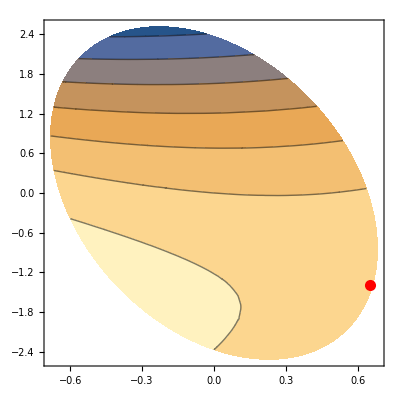

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
g=RandomReal[{-1,1},m];
Δ=0.7;
Ω=ImplicitRegion[{x,y}.B.{x,y}≤Δ^2,{x,y}];
{pStarBI}=NArgMin[{0.5*p.A.p+g.p,p.B.p≤Δ^2},p]
pCP=LinearSolve[A,-g];
M0=ArrayFlatten[({{{{Δ^2}}, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})];
M1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
M0Twiddle=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1Twiddle=ArrayFlatten[({{0, B}, {B, 0}})];
Max[Eigenvalues[{M0Twiddle,M1Twiddle}]]
ContourPlot[0.5*{x,y}.A.{x,y}+g.{x,y},{x,y}∈Ω,
Epilog->{{Red,PointSize[0.02],Point[pCP]}}]
```

## Constraints in 3D

Assuming the center point is at a point p. Compute the nearest points on the planes using calc stuff. I have normalized the descriptions of the plane to keep the formulas simple.

```mathematica
{b1,b2}={0.2,0.7};
{n1,n2}=Map[Normalize,{{1.0,0,-3},{1.6,2.4,1}}];
R=2;
p={0.2,0.3,0.4};
{t1,t2}=-{b1,b2};
Show[
ContourPlot3D[ {b1+n1.({x,y,z}-p)==0,b2+n2.({x,y,z}-p)==0},
{x,-R,R},{y,-R,R},{z,-R,R},
ContourStyle->{Directive[Yellow,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],
ParametricPlot3D[{p+t*n1,p+t*n2},{t, -R,R},PlotStyle->{Yellow, Blue}],
Graphics3D[{PointSize[0.02],
{Red,Point[p]},
{Yellow, Point[ p+t1*n1]},
{Blue, Point[p+t2*n2]}
}],
PlotLabel->{t1,t2}
]
```

-Graphics3D-

The nearest constraint is the yellow one! It is 0.2 from the yellow constraint.  The second nearest constraint is the blue one.  It is 0.5 from the blue constraint. I already sorted them so the nearest constraint is yellow.  Build spheres for each constraint.

```mathematica
Show[
ContourPlot3D[ {b1+n1.({x,y,z}-p)==0,b2+n2.({x,y,z}-p)==0,
Norm[{x,y,z}-p]==-t1,
Norm[{x,y,z}-p]==-t2
},
{x,-R,R},{y,-R,R},{z,-R,R},
ContourStyle->{Directive[Yellow,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],
ParametricPlot3D[{p+t*n1,p+t*n2},{t, -3,3},PlotStyle->{Yellow, Blue}],
Graphics3D[{PointSize[0.02],
{Red,Point[p]},
{Yellow, Point[ p+t1*n1]},
{Blue, Point[p+t2*n2]}
}],
PlotLabel->{t1,t2}
]
```

-Graphics3D-

What we want to do is to make an ellipsoid (defined by a B matrix just like the GEV-TRS paper) that respects both constraints and a trust region radius of say rMax. First thing is to understand how to represent a matrix for an ellipse.

```mathematica
Show[
ContourPlot3D[ {b1+n1.({x,y,z}-p)==0,b2+n2.({x,y,z}-p)==0,
1/t1^2({x,y,z}-p).({x,y,z}-p)==1,
1/t2^2({x,y,z}-p).({x,y,z}-p)==1},
{x,-R,R},{y,-R,R},{z,-R,R},
ContourStyle->{Directive[Yellow,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],
ParametricPlot3D[{p+t*n1,p+t*n2},{t, -3,3},PlotStyle->{Yellow, Blue}],
Graphics3D[{PointSize[0.02],
{Red,Point[p]},
(*{Red, Ellipsoid[p,B]},*)
{Yellow, Point[ p+t1*n1]},
{Blue, Point[p+t2*n2]}
}],
PlotLabel->{t1,t2}
]
```

-Graphics3D-

To make an ellipsoid that respects both constraints and a trust region radius rMax.  We keep the nearest constraint direction (assuming we have ordered the constraints appropriately this is n_1) and modify the second direction to be perpendicular to the first direction.   We are going to call the new orthogonal directions q_1 and q_2.

```mathematica
rMax=0.9;
q1=n1;
q2=Normalize[n2-(n2.q1) q1];
B=rMax^2*IdentityMatrix[3]+(t1^2-rMax^2)KroneckerProduct[q1,q1]+(t2^2-rMax^2)KroneckerProduct[q2,q2];
Show[
ContourPlot3D[ {b1+n1.({x,y,z}-p)==0,b2+n2.({x,y,z}-p)==0},
{x,-R,R},{y,-R,R},{z,-R,R},
ContourStyle->{Directive[Yellow,Opacity[0.5]],Directive[Blue,Opacity[0.5]]}],
ParametricPlot3D[{p+t*n1,p+t*n2},{t, -3,3},PlotStyle->{Yellow, Blue}],
Graphics3D[{PointSize[0.02],
{Red,Point[p]},
(*{Red, Ellipsoid[p,B]},*)
{Yellow, Point[ p+t1*n1]},
{Blue, Point[p+t2*n2]},
{Directive[Pink,Opacity[0.5]],Ellipsoid[p,B]}
}],
PlotLabel->√Eigenvalues[B]
]
```

-Graphics3D-

```mathematica
Inverse[B]
```

{{3.87865,0.369015,-7.04045},{0.369015,1.74355,0.123005},{-7.04045,0.123005,22.6532}}

```mathematica
InvB=1/rMax^2*IdentityMatrix[3]+(1/t1^2-1/rMax^2)KroneckerProduct[q1,q1]+(1/t2^2-1/rMax^2)KroneckerProduct[q2,q2]
```

{{3.87865,0.369015,-7.04045},{0.369015,1.74355,0.123005},{-7.04045,0.123005,22.6532}}

Code

## Build B Automatically

The input is a list of values 
	{
	{g_1,∇g_1},
	…
	{g_c,∇g_c}
	}
and a trust region radius Δ.  The output should be a list of orthogonal directions q_1…,q_a and a list of scalars α_1,…,α_a which define B as 
	B=1/Δ(I_m-∑_(i=1)^a q_i⊗q_i)+∑_(i=1)^a α_a q_i⊗q_i=1/Δ I + ∑_(i=1)^a (α_a-1/Δ)q_i⊗q_i
with the condition that the elliptical constraint region
	Ω_e={p∈ℝ^m: p.B.p≤1}
is contained in the original feasible region
	Ω={p∈ℝ^m: g_i+∇g_i.p≥0 for 1≤i≤c}.

The plan is to sort the constraints by distance to the boundary and construct B by projecting out the directions as shown above.

```mathematica
BuildB[gDgIn_List,Δ_Real]:=Module[{gDg,Q,R},
gDg=Select[ gDgIn, Abs[#⟦1⟧]/Norm[#⟦2⟧] <Δ &];
gDg=Sort[gDg,Abs[#1⟦1⟧ ]/Norm[#1⟦2⟧]<Abs[#2⟦1⟧]/Norm[#2⟦2⟧]&];
{Q,R}=QRDecomposition[gDg⟦All,2⟧];
Table[{Q⟦i⟧,Q⟦i⟧.gDg⟦i,2⟧},{i,Length[gDg]}]
]
```

```mathematica
?Select
```

Some visual testing

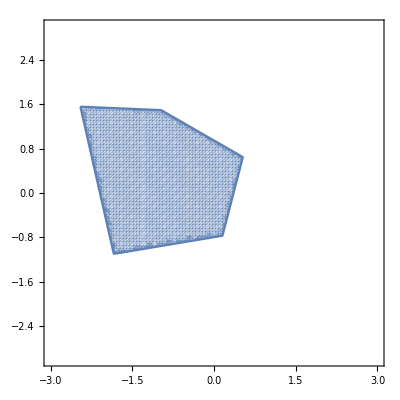

```mathematica
m=2;
c=12;
Δ=0.2;
{gMin,gMax}={0.001,4};
gDg=Table[{RandomReal[{gMin,gMax}], RandomReal[{-1,1},m]},c];
LinInEqs =Apply[And,Table[ {g, Dg}=gDg⟦i⟧;
g+Dg.{p1,p2}≥0,{i, Length[gDg]}]];
RegionPlot[LinInEqs,
{p1,-3,3},{p2,-3,3},PlotPoints->100]
```

More visual testing

```mathematica
m=3;
c=12;
Δ=0.2;
{gMin,gMax}={0.001,4};
gDg=Table[{RandomReal[{gMin,gMax}], RandomReal[{-1,1},m]},c];
LinInEqs =Apply[And,Table[ {g, Dg}=gDg⟦i⟧;
g+Dg.{p1,p2,p3}≥0,{i, Length[gDg]}]];
RegionPlot3D[
LinInEqs,
{p1,-3,3},{p2,-3,3},{p3,-3,3},
PlotPoints->100]
```

-Graphics3D-

Automatic testing using RegionWitin

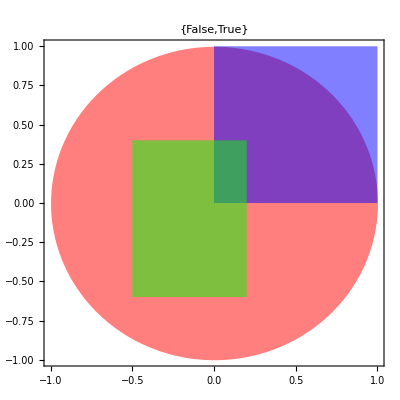

```mathematica
Ω1=Disk[];
Ω2=Rectangle[];
Ω3=Rectangle[{-0.5,-0.6},{0.2,0.4}];
Graphics[{
Opacity[0.5],
{Red,Ω1},
{Blue,Ω2},
{Green,Ω3}
},Frame->True,
PlotLabel->{RegionWithin[Ω1,Ω2],RegionWithin[Ω1,Ω3]}]
```